# My first notebook

08/08/2017 
Peter Manshausen

```mathematica
2+3
```

```mathematica
BaseForm[5,2]
```

```mathematica
PrimeQ[5]
```

```mathematica
5*2-8/2+6^2
```

```mathematica
1/(3*2)
```

```mathematica
x=5
```

```mathematica
?x
```

```mathematica
x=.
```

```mathematica
?x
```

```mathematica
p=1.5
x=6
3x
x^3.1
x/p
x^(3p)
```

```mathematica
3z
```

```mathematica
z=5
```

```mathematica
3z
```

```mathematica
a=1
b=5
ab
ba
a b
b a
```

```mathematica
x=.
```

```mathematica
f[x_]:=x^2
```

```mathematica
?f
```

```mathematica
f[4]
```

```mathematica
f[Pi]
```

```mathematica
π^2
```

```mathematica
f[1.6]
```

```mathematica
u=66
f[u]
```

```mathematica
g[x_]:=f[x]/Sin[x]
```

```mathematica
g[Pi/2]
```

```mathematica
f1[x_]:=(x+6) (x+1)
```

```mathematica
f1[2]
```

```mathematica
N[Pi, 50];
(*comment*)
```

```mathematica
ΟΒΑΓΡΥζϕιζηΥυϕΦΦχΧψΨωϑϱ℧Ϟ
```

ΟΒΑΓΡΥζϕιζηΥυϕΦΦχΧψΨωϑϱ℧Ϟ

```mathematica
x1=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
x2=Table[f[i], {i, 1, 11,2}]
```

{1,9,25,49,81,121}

```mathematica
x2={1,5,3,5}
```

{1,5,3,5}

```mathematica
?x2
```

Global`x2

x2={1,5,3,5}

```mathematica
myList=Table[{i,i^2}, {i,10,20}]
```

{{10,100},{11,121},{12,144},{13,169},{14,196},{15,225},{16,256},{17,289},{18,324},{19,361},{20,400}}

```mathematica
TableForm[myList]
```

10 | 100
11 | 121
12 | 144
13 | 169
14 | 196
15 | 225
16 | 256
17 | 289
18 | 324
19 | 361
20 | 400

```mathematica
myList//TableForm
```

10 | 100
11 | 121
12 | 144
13 | 169
14 | 196
15 | 225
16 | 256
17 | 289
18 | 324
19 | 361
20 | 400

```mathematica
Range[1,11,2]
```

{1,3,5,7,9,11}

```mathematica
Table[Prime[i],{i, 1,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
invest[n_]:=1000*1.05^n
years=Range[5]
invest[years]
```

{1,2,3,4,5}

{1050.,1102.5,1157.63,1215.51,1276.28}

```mathematica
years//invest
```

{1050.,1102.5,1157.63,1215.51,1276.28}

```mathematica
t=Table[{x, Sin[x]},{x,0,2Pi,Pi/4}]
```

{{0,0},{π/4,1/(√2)},{π/2,1},{(3 π)/4,1/(√2)},{π,0},{(5 π)/4,-1/(√2)},{(3 π)/2,-1},{(7 π)/4,-1/(√2)},{2 π,0}}

```mathematica
N[t,3]
```

{{0,0},{0.785,0.707},{1.57,1.},{2.36,0.707},{3.14,0},{3.93,-0.707},{4.71,-1.},{5.5,-0.707},{6.28,0}}

```mathematica
myList=Table[Fibonacci[n], {n,1,50}]
myList[[10]]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887,9227465,14930352,24157817,39088169,63245986,102334155,165580141,267914296,433494437,701408733,1134903170,1836311903,2971215073,4807526976,7778742049,12586269025}

55

```mathematica
Dimensions[myList]
```

{50}

```mathematica
Select[myList, PrimeQ]
```

{2,3,5,13,89,233,1597,28657,514229,433494437,2971215073}

```mathematica
Plot[Fibonacci[x],{x, 1,10}]
```

```mathematica
a=Table[i,{i,5}]
b=a^2
```

{1,2,3,4,5}

{1,4,9,16,25}

```mathematica
Join[a,b]
```

{1,2,3,4,5,1,4,9,16,25}

```mathematica
Union[a,b]
```

{1,2,3,4,5,9,16,25}

```mathematica
Intersection[a,b]
```

{1,4}

```mathematica
c={a,6,7}
d={b,36,49}
```

{{1,2,3,4,5},6,7}

{{1,4,9,16,25},36,49}

```mathematica
e=Flatten[d]
f=Flatten[c]
```

{1,4,9,16,25,36,49}

{1,2,3,4,5,6,7}

```mathematica
Join[f,e]
```

{1,2,3,4,5,6,7,1,4,9,16,25,36,49}

```mathematica
g={f,e}
```

{{1,2,3,4,5,6,7},{1,4,9,16,25,36,49}}

```mathematica
Transpose[g]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49}}

```mathematica
TableForm[Transpose[g]]
```

```mathematica
{{1, 1}, {2, 4}, {3, 9}, {4, 16}, {5, 25}, {6, 36}, {7, 49}}
```

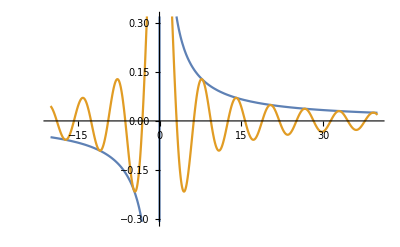

```mathematica
Plot[{1/x,Sinc[x]},{x,-20,40}]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

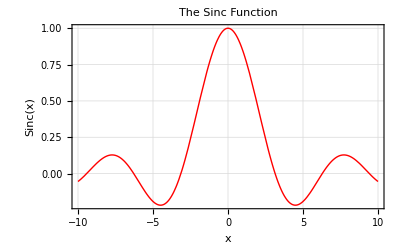

```mathematica
Plot[Sinc[x], {x,-10,10}, PlotStyle->{Red, Thick}, PlotLabel-> "The Sinc Function", Frame->True, FrameLabel->{"x", "Sinc(x)"}, GridLines->Automatic]
```

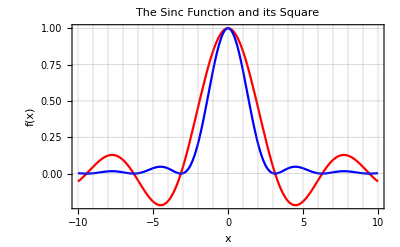

```mathematica
Plot[Tooltip[{Sinc[x], Sinc[x]^2}, "Sinc[x], Sinc[x]^2"], {x,-10,10}, PlotStyle->{Red,Blue, Thick}, PlotLabel-> "The Sinc Function and its Square", Frame->True, FrameLabel->{"x", "f(x)"}, GridLines->{Range[-10,10,1], Range[-.25,1,.25]}]
```

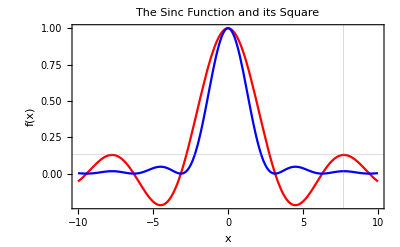

```mathematica
Plot[Tooltip[{Sinc[x], Sinc[x]^2}, "Sinc[x], Sinc[x]^2"], {x,-10,10}, PlotStyle->{Red,Blue, Thick}, PlotLabel-> "The Sinc Function and its Square", Frame->True, FrameLabel->{"x", "f(x)"}, GridLines->{{7.7}, {0.13}}]
```

```mathematica
myProfile=Table[{{x,RandomReal[{0.8,1.2}]Exp[-0.1x^2]}, ErrorBar[0.1]},{x,-10,10,0.5}]
```

{{{-10.,0.0000502519},ErrorBar[0.1]},{{-9.5,0.000123863},ErrorBar[0.1]},{{-9.,0.000359534},ErrorBar[0.1]},{{-8.5,0.000836178},ErrorBar[0.1]},{{-8.,0.00142579},ErrorBar[0.1]},{{-7.5,0.00384753},ErrorBar[0.1]},{{-7.,0.0063578},ErrorBar[0.1]},{{-6.5,0.0159583},ErrorBar[0.1]},{{-6.,0.0290464},ErrorBar[0.1]},{{-5.5,0.0518066},ErrorBar[0.1]},{{-5.,0.0787465},ErrorBar[0.1]},{{-4.5,0.153103},ErrorBar[0.1]},{{-4.,0.208862},ErrorBar[0.1]},{{-3.5,0.315708},ErrorBar[0.1]},{{-3.,0.398707},ErrorBar[0.1]},{{-2.5,0.459895},ErrorBar[0.1]},{{-2.,0.653183},ErrorBar[0.1]},{{-1.5,0.674174},ErrorBar[0.1]},{{-1.,0.735359},ErrorBar[0.1]},{{-0.5,0.988463},ErrorBar[0.1]},{{0.,0.94216},ErrorBar[0.1]},{{0.5,0.987296},ErrorBar[0.1]},{{1.,0.786821},ErrorBar[0.1]},{{1.5,0.929376},ErrorBar[0.1]},{{2.,0.744462},ErrorBar[0.1]},{{2.5,0.633926},ErrorBar[0.1]},{{3.,0.358411},ErrorBar[0.1]},{{3.5,0.336767},ErrorBar[0.1]},{{4.,0.174894},ErrorBar[0.1]},{{4.5,0.137925},ErrorBar[0.1]},{{5.,0.0957027},ErrorBar[0.1]},{{5.5,0.0578243},ErrorBar[0.1]},{{6.,0.0309212},ErrorBar[0.1]},{{6.5,0.0170323},ErrorBar[0.1]},{{7.,0.00889834},ErrorBar[0.1]},{{7.5,0.00413205},ErrorBar[0.1]},{{8.,0.00135457},ErrorBar[0.1]},{{8.5,0.000725643},ErrorBar[0.1]},{{9.,0.000346714},ErrorBar[0.1]},{{9.5,0.000130117},ErrorBar[0.1]},{{10.,0.000042986},ErrorBar[0.1]}}

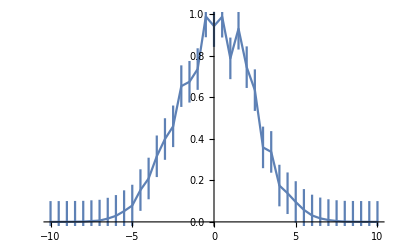

```mathematica
ErrorListPlot[myProfile, Joined->True]
```

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
myProfile1=Table[{x,RandomReal[{0.8,1.2}]Exp[-0.1x^2]},{x,-10,10,0.5}];
a=.
b=.
```

```mathematica
sol=FindFit[myProfile1, a Exp[-b x^2], {a,b}, x]
```

{a→1.02484,b→0.0979027}

```mathematica
a Exp[-b x^2]/.{a->1.0248372059795834,b->0.09790270319403682}
```

1.02484 ⅇ^(-0.0979027 x^2)

```mathematica
myFit[x_]:=a Exp[-b x^2]/.sol
```

```mathematica
myFit[1]
```

0.929258

```mathematica
/.
```

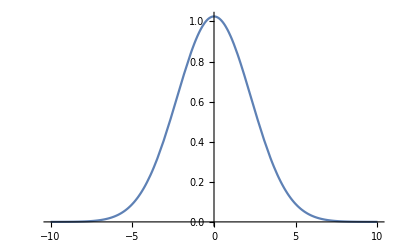

```mathematica
Plot[myFit[x], {x,-10,10}]
```

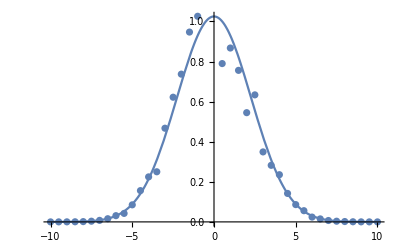

```mathematica
Show[Plot[myFit[x], {x,-10,10}],ListPlot[myProfile1]]
```

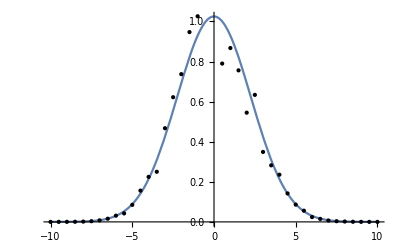

```mathematica
Plot[myFit[x], {x,-10,10}, Epilog->Point[myProfile1]]
```

```mathematica
Manipulate[Plot[Sin[5t+ ϕ], {t,0,2 Pi}], {ϕ, 0, 10 Pi}]
```

```mathematica
sincurve=.
sincurve[ϕ_]:=Sin[5t+ϕ]
Manipulate[Plot[sincurve[ϕ],{t,0,2Pi}],{ϕ,0,2Pi}]
```

```mathematica
ListPlot3D
```

```mathematica
Plot3D[Sin[x]^3Cos[y],{x,-2 Pi, 2Pi}, {y, -2Pi,2Pi}, PlotStyle->{Opacity[0.8]}]
```

-Graphics3D-

```mathematica
int[θ_]:=(BesselJ[1,10Sin[θ]]/(10Sin[θ]))^2
int[1]
```

1/100 BesselJ[1,10 Sin[1]]^2 Csc[1]^2

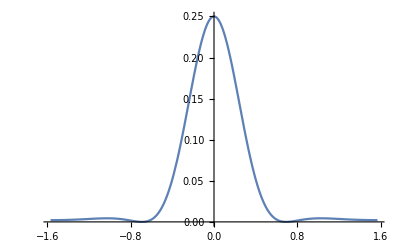

```mathematica
Plot[(BesselJ[1, 6 Sin[θ]]/( 6 Sin[θ]))^2, {θ,-Pi/2,Pi/2}]
```

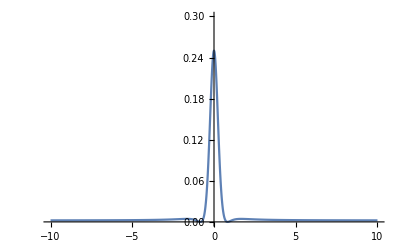

Plot::nonopt: Options expected (instead of {0, 0.3}) beyond position 2 in (FractionBox[BesselJ[1, Sin[θ[x]]], Sin[θ[x]]])^2. An option must be a rule or a list of rules. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/nonopt",
ButtonNote->"Plot::nonopt"]

```mathematica
θ[x_]:= ArcTan[x/1]
Plot[(BesselJ[1, 6Sin[θ[x]]]/( 6Sin[θ[x]]))^2, {x,-10,10}, PlotRange->{{-10,10}, {0,0.3}}]
```

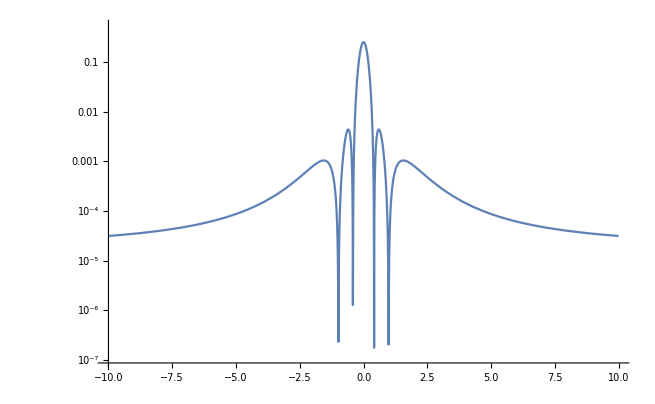

```mathematica
LogPlot[(BesselJ[1,10Sin[θ[x]]]/(10Sin[θ[x]]))^2,{x,-10,10},PlotRange->{{-10,10},{0,0.3}}]
```

```mathematica
FindMinimum[int[θ[x]],x]
```

```mathematica
{7.739073540659282*^-22,{x->0.984489400897955}}
Quantity[FindMinimum[int[θ[x]],x], "Meters"]
```

{7.73907×10^-22,{x→0.984489}}

{7.73907×10^-22 m,{(x→0.984489) m}}

```mathematica
ϕ2D[x_,y_]:= ArcTan[x^2+y^2]
```

```mathematica
Plot3D[(BesselJ[1, 10Sin[ϕ2D[x,y]]]/( 10Sin[ϕ2D[x,y]]))^2, {x,-10,10}, {y, -10,10}]
```

-Graphics3D-

```mathematica
Plot3D[(BesselJ[1,10 Sin[ϕ2D[x,y]]]/(10 Sin[ϕ2D[x,y]]))^2,{x,-2,2},{y,-2,2},PlotPoints->35,MaxRecursion->2,PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[(BesselJ[1,10 Sin[ϕ2D[x,y]]]/(10 Sin[ϕ2D[x,y]]))^2,{x,-2,2},{y,-2,2},Mesh->All,MeshFunctions->Automatic,PlotPoints->35,MaxRecursion->2,PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[(BesselJ[1,10 Sin[ϕ2D[x,y]]]/(10 Sin[ϕ2D[x,y]]))^2,{x,-2,2},{y,-2,2},Mesh->Automatic,MeshFunctions->{#3&},Mesh->All,MeshFunctions->Automatic,PlotPoints->35,MaxRecursion->2,PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[(BesselJ[1,10 Sin[ϕ2D[x,y]]]/(10 Sin[ϕ2D[x,y]]))^2,{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1.,0.72,1.],Opacity[0.644]],Mesh->Automatic,MeshFunctions->{#3&},PlotPoints->35,MaxRecursion->2,PlotRange->Full]
```

-Graphics3D-

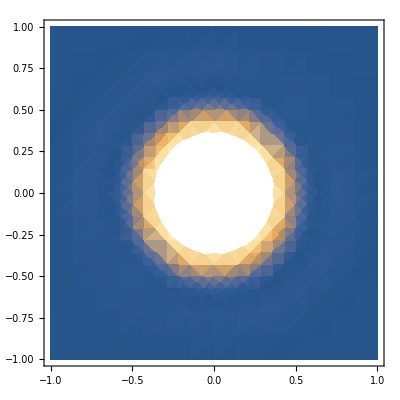

```mathematica
DensityPlot[int[ϕ2D[x,y]],{x,-1,1},{y,-1,1}]
```